```mathematica
sincos[theta_]:={Cos[theta], Sin[theta]};
```

```mathematica
$DetectorRadius=4;
```

```mathematica
temp={
{"Cz",{0,0}},

{"T4",40* sincos[0]},{"F8",40* sincos[Pi/5]},{"Fp2",40* sincos[Pi*2/5]},
{"Fp1",40* sincos[Pi*3/5]},{"F7",40* sincos[Pi*4/5]},{"T3",40* sincos[Pi]},
{"T5",40* sincos[Pi*6/5]},{"O1",40* sincos[Pi*7/5]},
{"O2",40* sincos[Pi*8/5]},{"T6",40* sincos[Pi*9/5]},

{"C4",20* sincos[0]},{"Fz",20* sincos[Pi/2]},
{"C3",20* sincos[Pi]},{"Pz",20* sincos[Pi*3/2]},

{"F4",{15/79 (-27+29 √5+2 √(325+122 √5)),15/79 (21-5 √5+3 √(730+82 √5))}},{"F3",{-15/79 (-27+29 √5+2 √(325+122 √5)),15/79 (21-5 √5+3 √(730+82 √5))}},
{"P4",{15/79 (-27+29 √5+2 √(325+122 √5)),-15/79 (21-5 √5+3 √(730+82 √5))}},
{"P3",{-15/79 (-27+29 √5+2 √(325+122 √5)),-15/79 (21-5 √5+3 √(730+82 √5))}}

};
```

```mathematica
$ChannelCoordinates={#[[1]],N[#[[2]]]}& /@temp
```

{{Cz,{0.,0.}},{T4,{40.,0.}},{F8,{32.3607,23.5114}},{Fp2,{12.3607,38.0423}},{Fp1,{-12.3607,38.0423}},{F7,{-32.3607,23.5114}},{T3,{-40.,0.}},{T5,{-32.3607,-23.5114}},{O1,{-12.3607,-38.0423}},{O2,{12.3607,-38.0423}},{T6,{32.3607,-23.5114}},{C4,{20.,0.}},{Fz,{0.,20.}},{C3,{-20.,0.}},{Pz,{0.,-20.}},{F4,{16.4707,19.0794}},{F3,{-16.4707,19.0794}},{P4,{16.4707,-19.0794}},{P3,{-16.4707,-19.0794}}}

```mathematica
$FramePlotBackground[]:=
Graphics[ 
{White,EdgeForm[Thick],
Disk[{-50,0},10],Disk[{50,0},10],
Black, Disk[{0,20},40],
White,Disk[{0,0},50]},
BaseStyle->{FontFamily->"Helvetica"}
]
```

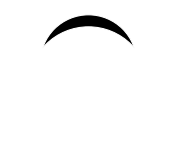

```mathematica
$FramePlotBackground[]
```

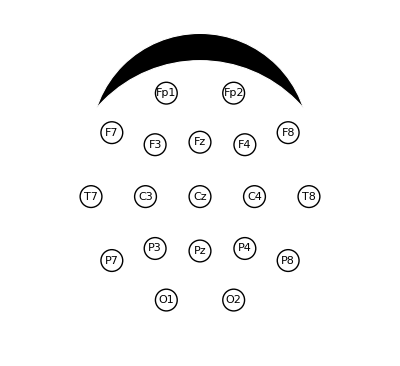

```mathematica
Show[$FramePlotBackground[],
Graphics[
{Circle[#[[2]],$DetectorRadius]& /@$ChannelCoordinates,
Text[#[[1]],#[[2]]]& /@$ChannelCoordinates}]
]
```

```mathematica
channels=$ChannelCoordinates[[All,1]]
```

{Cz,T8,F8,Fp2,Fp1,F7,T7,P7,O1,O2,P8,C4,Fz,C3,Pz,F4,F3,P4,P3}

```mathematica
$GetChannelCoordinates[channel_String]:=
Module[{pos},
pos=Flatten[Position[channels, "F7"]];
If[Length[pos]==0, Message[$GetChannelCoordinates::noSuchChannel, channel],
channelCoordinates[[pos[[1]], 2]]]
];
```

```mathematica
$GetChannelCoordinates::noSuchChannel="The specified channel `1` was not found in the current layout!";
```

```mathematica
$GetChannelCoordinates["F7"]
```

{-32.3607,23.5114}

## Calculate F4 Location

### Line connecting Fz and F8

```mathematica
temp[[13]]
```

{Fz,{0,20}}

```mathematica
temp[[3]]
```

{F8,{10 (1+√5),40 √(5/8-(√5)/8)}}

```mathematica
Solve[Norm[{x,y}-{0,20}]==Norm[{x,y}-{10 (1+√5),40 √(5/8-(√5)/8)}],y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→(600-200 √5-Abs[x]^2+Abs[-10 (1+√5)+x]^2)/(20 (-2+√(2 (5-√5))))}}

### Line connecting Fp2 and C4

```mathematica
temp[[4]]
```

{Fp2,{10 (-1+√5),40 √(5/8+(√5)/8)}}

```mathematica
temp[[12]]
```

{C4,{20,0}}

```mathematica
Solve[Norm[{x,y}-{10 (-1+√5),40 √(5/8+(√5)/8)}]==Norm[{x,y}-{20,0}],y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→(1000+200 √5-Abs[-20+x]^2+Abs[-10 (-1+√5)+x]^2)/(20 √(2 (5+√5)))}}

### Intersection

```mathematica
Solve[(600-200 √5-Abs[x]^2+Abs[-10 (1+√5)+x]^2)/(20 (-2+√(2 (5-√5))))==(1000+200 √5-Abs[-20+x]^2+Abs[-10 (-1+√5)+x]^2)/(20 √(2 (5+√5))),x]
```

{{x→(60 (√2-√(5-√5)+√(5+√5)))/(-3 √2+√10+3 √(5-√5)-√(5 (5-√5))+√(5+√5)+√(5 (5+√5)))}}

```mathematica
FullSimplify[(60 (√2-√(5-√5)+√(5+√5)))/(-3 √2+√10+3 √(5-√5)-√(5 (5-√5))+√(5+√5)+√(5 (5+√5)))]
```

15/79 (-27+29 √5+2 √(325+122 √5))

```mathematica
FullSimplify[(1000+200 √5-Abs[-20+x]^2+Abs[-10 (-1+√5)+x]^2)/(20 √(2 (5+√5))) /.x->15/79 (-27+29 √5+2 √(325+122 √5))]
```

15/79 (21-5 √5+3 √(730+82 √5))